```mathematica
-Graphics-;
```

```mathematica
Pje=f∫_0^(1/f) (Δt 2π f Cos[2π f τ])^2 ⅆτ
```

2 f^2 π^2 Δt^2

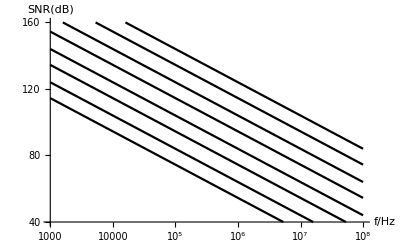

```mathematica
snr[Δt_,f_]:=1/(4 π^2 f^2 Δt^2);
snrdb[Δt_,f_]:=10*Log10[snr[Δt,f]];
dt={0.1×10^-12,0.3×10^-12,1×10^-12,3×10^-12,10×10^-12,30×10^-12,100×10^-12,300×10^-12};
LogLinearPlot[snrdb[dt,f],{f,1000,100000000},Ticks->{Automatic,{40,60,80,100,120,140,160}},PlotRange->{40,160},PlotTheme->"Monochrome",GridLines->Automatic,AxesLabel->{"f/Hz","SNR(dB)"},LabelStyle->(FontFamily->"Courier New")]
```

```mathematica
N[snrdb[10×10^-12,10000000]]
```

64.0364

```mathematica
N[20*Log10[1/(2*π*10000000*10×10^-12)]]
```

64.0364

```mathematica
20*log(2*pi*10e6*1e-9/2/sqrt(2)*0.01)
```